Variational Quantum Classifier: Iris

Amplitude Embedding: Methodpaclet:QuantumMob/QuantumPlaybook/tutorial/VariationalQuantumClassifierIris#1429043704 | Quantum Circuit Layerpaclet:QuantumMob/QuantumPlaybook/tutorial/VariationalQuantumClassifierIris#75111769
Datapaclet:QuantumMob/QuantumPlaybook/tutorial/VariationalQuantumClassifierIris#1388635064 | Optimizationpaclet:QuantumMob/QuantumPlaybook/tutorial/VariationalQuantumClassifierIris#1684028550

This demonstration is a translation of the tutorial “Variational classifierhttps://pennylane.ai/qml/demos/tutorial_variational_classifier” in PennyLane by Maria Schuld. It demonstrates variational quantum classifiers; that is, quantum circuits that can be trained from labelled data to classify new data samples.

In particular, we will see how to encode real vectors as amplitude vectors (amplitude encoding) and train the model to recognize the first two classes of flowers in the Iris dataset.

AmplitudeEmbeddingpaclet:QuantumMob/Q3S/ref/AmplitudeEmbeddingQuantumMob Package Symbol | Encodes data into amplitudes of a quantum state
AmplitudeEmbeddingGatepaclet:QuantumMob/QuantumPlaybook/ref/AmplitudeEmbeddingGateQuantumMob Package Symbol | Quantum circuit model to implement amplitude embedding
FindMinimumpaclet:ref/FindMinimum | Find the minimum of a function

Frequently used function in variational classification.

Make sure to load the Q3 package.

```mathematica
Needs["QuantumMob`Q3S`"]
```

Amplitude Embedding: Method

```mathematica
Let[Qubit,S]
```

```mathematica
$n=2;
$N=Power[2,$n];
kk=Range[$n];
SS=S[kk,$]
```

{S_(,,1),S_(,,2)}

Get the data.

```mathematica
aa=Normalize@RandomReal[{0,1},$N]
```

{0.18426,0.535389,0.670164,0.479883}

Embed the data into a quantum state.

```mathematica
in=AmplitudeEmbedding[aa,SS]
```

0.18426 0_(,,S_(,,1))0_(,,S_(,,2))+0.535389 0_(,,S_(,,1))1_(,,S_(,,2))+0.670164 1_(,,S_(,,1))0_(,,S_(,,2))+0.479883 1_(,,S_(,,1))1_(,,S_(,,2))

### Quantum circuit implementation

Embedding the data into a quantum state as above on actual quantum computer is not trivial. One implementation based on quantum circuit model may be achieved by the following function.

```mathematica
op=AmplitudeEmbeddingGate[aa,SS]
```

AmplitudeEmbeddingGate[{0.18426,0.535389,0.670164,0.479883},{S_(,,1),S_(,,2)}]

```mathematica
QuantumCircuit[op]
```

-Graphics-

More explicitly, the above quantum circuit is equivalent to the following.

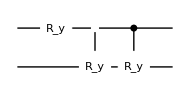

```mathematica
QuantumCircuit[ExpandAll@op]
```

The above quantum circuit may be further simplified.

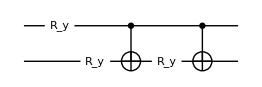

```mathematica
qc=QuantumCircuit[GateFactor/@Expand@op]
```

```mathematica
new=qc**Ket[SS]//Chop
```

0.18426 0_(,,S_(,,1))0_(,,S_(,,2))+0.535389 0_(,,S_(,,1))1_(,,S_(,,2))+0.670164 1_(,,S_(,,1))0_(,,S_(,,2))+0.479883 1_(,,S_(,,1))1_(,,S_(,,2))

```mathematica
Fidelity[new,in]
```

1.

Data

### Data loading and embedding

Import the iris date and check the first three entries.

```mathematica
raw=Import[PacletObject["QuantumPlaybook"]["AssetLocation","Iris"],"Table"];
raw=Map[Most[#]->Round[Last@#]&,raw];
raw[[;;3]]
```

{{0.399999999999999911,0.75,0.199999999999999956,0.0500000000000000028}→-1,{0.300000000000000267,0.5,0.199999999999999956,0.0500000000000000028}→-1,{0.200000000000000178,0.600000000000000089,0.150000000000000022,0.0500000000000000028}→-1}

Renormalize the data.

```mathematica
data=Thread[Map[Normalize@Join[Take[#,2],0.3{1,0}]&,Keys@raw]->Values[raw]];
data[[1]]
```

{0.44376,0.83205,0.33282,0.}→-1

Here, vector representation is nothing but the input data itself since we just simulate the amplitude embedding.

```mathematica
(*
in=AmplitudeEmbedding[#,SS]&/@Keys[data]//Chop;
in=Matrix[in,SS];
*)
$in=Keys[data];
```

### Features

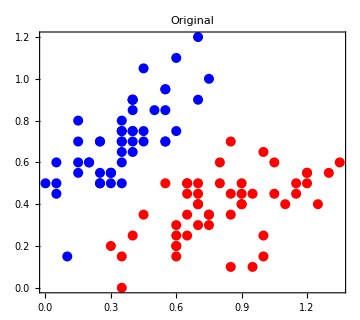

```mathematica
gg=Map[Take[#,2]&,GroupBy[raw,Last,Map[First]],{2}];
Graphics[{PointSize[0.02],Red,Point/@gg[1],Blue,Point/@gg[-1]},
PlotLabel->"Original",
ImageSize->Medium,
Frame->True]
```

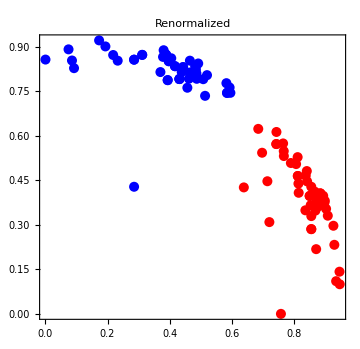

```mathematica
gg=Map[Take[#,2]&,GroupBy[data,Last,Map[First]],{2}];
Graphics[{PointSize[0.02],Red,Point/@gg[1],Blue,Point/@gg[-1]},
PlotLabel->"Renormalized",
ImageSize->Medium,
Frame->True]
```

```mathematica
RR=AmplitudeEmbeddingGate[#,SS]&/@Keys[data][[;;,;;-2]];
RR=List@@@Map[GateFactor,Expand/@RR,{2}]/.{CNOT->Nothing};
angles=Map[RotationAngle,RR, {2}];
```

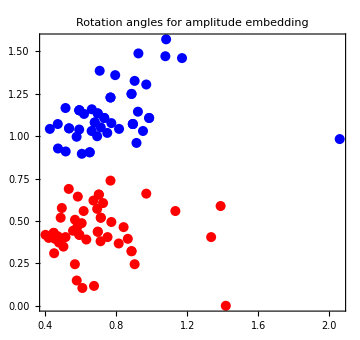

```mathematica
tf=Positive[Values@data]//Flatten;
aa=Pick[angles[[;;,;;2]],tf];
bb=Pick[angles[[;;,;;2]],Not/@tf];
Graphics[{PointSize[0.02],Red,Point/@aa,Blue,Point/@bb},
PlotLabel->"Rotation angles for amplitude embedding",
ImageSize->Medium,
Frame->True]
```

Quantum Circuit Layer

Construct the basic quantum circuit layer to use.

```mathematica
Let[Real,w]
```

```mathematica
layer[lyr_Integer]:=QuantumCircuit[
Table[EulerRotation[w[lyr,k,{1,2,3}],S[k,$]],{k,$n}],
CNOT[S[1],S[2]]
]
layer[ll:{__Integer}]:=Apply[QuantumCircuit,layer/@ll]
```

Check it by show two layers.

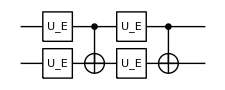

```mathematica
layer[{1,2}]
```

Optimization

### Using three layers

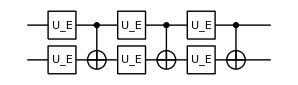

```mathematica
$L=3;
$layer=layer[Range@$L]
$mat=Normal@Matrix[$layer,SS];
```

```mathematica
ww=w[Range@$L,Range@$n,{1,2,3}];
constraints=Thread[0<=ww<Pi];
```

```mathematica
w0=Flatten@RandomReal[{0,1}*Pi,{$L,$n,3}];
```

```mathematica
Z1=Matrix[S[1,3],SS];
```

```mathematica
Clear[optimizer]
optimizer[w0_]:=Module[
{ii=RandomChoice[Range@Length@data,4],
yy,vv,avg,sol,cost},
yy=Part[Values@data,ii];
vv=Transpose@Part[$in,ii];
vv=Transpose[$mat.vv];
avg=Map[Conjugate[#].Z1.#&,vv];
cost=Mean@Abs[avg-yy]^2;
EchoTiming[
{cost,sol}=FindMinimum[{cost,constraints},Transpose@{ww,w0},
StepMonitor:>PrintTemporary["Cost: ",cost],
Method->"IPOPT"];
];
Echo[{Chop[avg/.sol],yy,cost},"{avg, yy, cost}"];
Return[ww/.sol]
]
```

```mathematica
optimizer[w0]
```

1.12056

{avg, yy, cost}  {{0.760846,-0.716791,-0.392067,0.252894},{1,-1,-1,1},0.22029}

{1.0661,0.334111,0.671318,3.14032,1.61577,0.0280648,1.03531,1.24874,1.71972,1.50162,2.28669,1.53419,2.09449,2.20327,1.96039,2.17165,1.51406,0.841476}

Find the optimal values of the parameters iteratively.

```mathematica
$R=5;(* the number of iterations *)
new=Nest[optimizer,w0,$R]
```

1.88741

{avg, yy, cost}  {{0.905139,0.999223,0.861843,0.236837},{1,1,1,-1},0.135173}

0.711994

{avg, yy, cost}  {{-0.997963,-0.995693,-0.999685,-0.983982},{-1,-1,-1,-1},0.0000321422}

0.786509

{avg, yy, cost}  {{-0.572712,-0.572712,0.582443,0.560302},{-1,-1,1,1},0.183148}

0.972399

{avg, yy, cost}  {{-0.965823,-0.882765,-0.967971,-0.214733},{-1,-1,-1,1},0.122181}

0.951594

{avg, yy, cost}  {{0.892343,0.844728,0.995771,-0.48356},{1,1,1,-1},0.0383766}

{0.974371,1.30963,1.57841,1.50559,1.33365,2.93231,0.118948,1.24401,0.778738,2.65051,2.58627,0.67015,1.5958,1.49835,0.118958,1.60183,1.57315,1.51935}

From the optimized parameters, make predictions.

```mathematica
mm=$mat/.Thread[ww->new];
```

```mathematica
vv=Transpose[mm.Transpose[$in]];
predicted=Map[Sign@Chop[Conjugate[#].Z1.#]&,vv]
```

{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,1,-1,-1,-1,1,-1,-1,-1,1,-1,1,-1,-1,-1,-1,1,-1,-1,1,-1,-1,1,-1,-1,-1,-1,1,-1,-1,-1,-1,1,-1,-1,-1,-1,-1,-1,-1,-1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
predicted-Values[data]
```

{0,0,0,0,0,0,0,0,0,0,2,0,0,0,2,0,0,0,2,0,2,0,0,0,0,2,0,0,2,0,0,2,0,0,0,0,2,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

### Using five layers

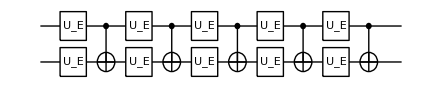

```mathematica
$L=5;
$layer=layer[Range@$L]
$mat=Normal@Matrix[$layer,SS];
```

```mathematica
ww=w[Range@$L,Range@$n,{1,2,3}];
constraints=Thread[0<=ww<Pi];
```

```mathematica
w0=Flatten@RandomReal[{0,1}*Pi,{$L,$n,3}];
```

```mathematica
Z1=Matrix[S[1,3],SS];
```

```mathematica
Clear[optimizer]
optimizer[w0_]:=Module[
{ii=RandomChoice[Range@Length@data,4],
yy,vv,avg,sol,cost},
yy=Part[Values@data,ii];
vv=Transpose@Part[$in,ii];
vv=Transpose[$mat.vv];
avg=Map[Conjugate[#].Z1.#&,vv];
cost=Mean@Abs[avg-yy]^2;
EchoTiming[
{cost,sol}=FindMinimum[{cost,constraints},Transpose@{ww,w0},
StepMonitor:>PrintTemporary["Cost: ",cost],
Method->"IPOPT"];
];
Echo[{Chop[avg/.sol],yy,cost},"{avg, yy, cost}"];
Return[ww/.sol]
]
```

```mathematica
optimizer[w0]
```

7.77664

{avg, yy, cost}  {{0.24822,0.852321,0.921564,0.998178},{-1,1,1,1},0.13619}

{0.546366,2.21511,0.482023,1.94012,2.59612,2.05643,0.577314,1.3536,0.636025,2.60852,2.4734,0.448774,0.800182,0.401077,1.24512,2.59658,2.3454,1.30989,2.14661,1.71464,2.27962,2.52994,1.27958,2.45989,2.12922,2.87295,0.662435,1.42999,2.22792,1.74868}

Find the optimal values of the parameters iteratively.

```mathematica
$R=5;(* the number of iterations *)
new=Nest[optimizer,w0,$R]
```

7.38266

{avg, yy, cost}  {{0.711461,-0.958077,-0.265327,0.820694},{1,-1,-1,1},0.0967895}

16.1616

{avg, yy, cost}  {{0.877783,0.28046,0.96727,0.973767},{1,-1,1,1},0.133524}

8.22169

{avg, yy, cost}  {{0.95975,0.925322,0.0396846,0.940586},{1,1,-1,1},0.0921163}

6.94808

{avg, yy, cost}  {{-0.628165,-0.365753,0.613414,0.407993},{-1,-1,1,1},0.246183}

4.11915

{avg, yy, cost}  {{-0.600738,0.999985,0.859093,0.955632},{-1,1,1,1},0.0213562}

{0.74076,1.41404,0.754153,1.52085,2.54255,2.32751,0.430348,0.666755,0.871047,2.3348,1.72308,1.08381,1.15361,0.55873,0.532939,1.44438,2.17979,1.55592,1.62013,0.723068,2.3005,2.51849,1.23921,2.32893,1.95656,1.82639,0.795109,1.47236,2.02174,1.69523}

From the optimized parameters, make predictions.

```mathematica
mm=$mat/.Thread[ww->new];
```

```mathematica
vv=Transpose[mm.Transpose[$in]];
predicted=Map[Sign@Chop[Conjugate[#].Z1.#]&,vv]
```

{1,1,-1,-1,-1,1,-1,-1,-1,1,1,-1,-1,-1,1,1,1,1,1,-1,1,-1,-1,1,-1,1,-1,1,1,-1,-1,1,-1,1,1,1,1,1,-1,1,-1,1,-1,-1,-1,-1,-1,-1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
predicted-Values[data]
```

{2,2,0,0,0,2,0,0,0,2,2,0,0,0,2,2,2,2,2,0,2,0,0,2,0,2,0,2,2,0,0,2,0,2,2,2,2,2,0,2,0,2,0,0,0,0,0,0,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

| Related Guides
▪Quantum Information Systems
▪Quantum Many-Body Systems
▪Quantum Spin Systems

| Related Tech Notes
▪A Quantum Playbook
▪Quantum Information Systems with Q3
▪Quantum Many-Body Systems with Q3
▪Quantum Spin Systems with Q3

| Related Links
Maria Should, PennyLane demonstration “Variational classifierhttps://pennylane.ai/qml/demos/tutorial_variational_classifier”.
▪Mahn-Soo Choi (2022)https://doi.org/10.1007/978-3-030-91214-7, A Quantum Computation Workbook (Springer, 2022).